```mathematica
Clear["`*"]
```

```mathematica
<<PlotLegends`
```

# Spencer Lyon

## Physics 330

Lab 3

## P3.2

### a.)

(γ (-ⅇ^(t (-√(γ^2-ω0^2)-γ)))+γ ⅇ^(t (√(γ^2-ω0^2)-γ))+√(γ^2-ω0^2) ⅇ^(t (-√(γ^2-ω0^2)-γ))+√(γ^2-ω0^2) ⅇ^(t (√(γ^2-ω0^2)-γ)))/(2 √(γ^2-ω0^2))

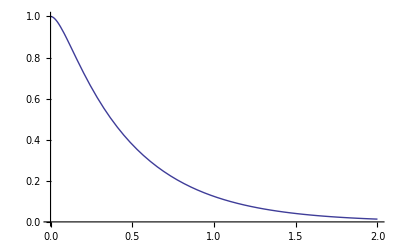

```mathematica
eqns = {D[y[t],{t,2}] == - ω0^2 * y[t] - 2 γ D[y[t],t], y[0]==1, y'[0]==0};
test = {γ->10, ω0->2π};
yPos = y[t]/.DSolve[eqns, y[t],t][[1]]
Plot[yPos/.test,{t,0,2}]
```

### b.)

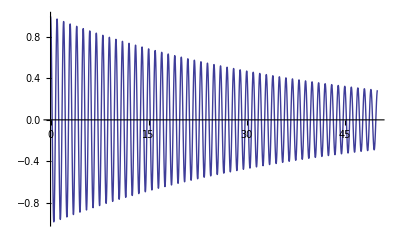

```mathematica
test2 = {γ->0.025, ω0->2π};
Plot[yPos/.test2,{t,0,50}]
```

### c.) NOT COMPLETE. ASK THEM WHAT THEY ARE LOOKING FOR.

```mathematica
Manipulate[
Plot[yPos/.{γ->gam, ω0->2π},{t,0,4},  PlotRange->{-1,1}], {gam, 0,15}]
```

## P3.3

-(F0 (γ ω^2 ⅇ^(t (-√(γ^2-ω0^2)-γ))-γ ω^2 ⅇ^(t (√(γ^2-ω0^2)-γ))+ω^2 √(γ^2-ω0^2) ⅇ^(t (-√(γ^2-ω0^2)-γ))+ω^2 √(γ^2-ω0^2) ⅇ^(t (√(γ^2-ω0^2)-γ))-2 ω^2 √(γ^2-ω0^2) cos(t ω)+4 γ ω √(γ^2-ω0^2) sin(t ω)+2 ω0^2 √(γ^2-ω0^2) cos(t ω)+γ ω0^2 ⅇ^(t (-√(γ^2-ω0^2)-γ))-γ ω0^2 ⅇ^(t (√(γ^2-ω0^2)-γ))-ω0^2 √(γ^2-ω0^2) ⅇ^(t (-√(γ^2-ω0^2)-γ))-ω0^2 √(γ^2-ω0^2) ⅇ^(t (√(γ^2-ω0^2)-γ))))/(2 √(γ^2-ω0^2) (2 γ √(γ^2-ω0^2)+2 γ^2+ω^2-ω0^2) (2 γ √(γ^2-ω0^2)-2 γ^2-ω^2+ω0^2))

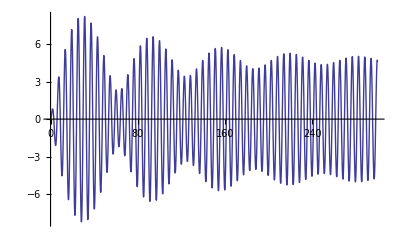

```mathematica
eqn37 = {D[y[t], {t,2}]== - ω0^2*y[t] - 2* γ* D[y[t],t] + F0* Cos[ω* t], y[0]==0, y'[0]==0};
test37 = {ω0->1, F0->1, ω->1.1, γ->0.01};
y37 = y[t]/.DSolve[eqn37, y[t],t][[1]]
Plot[y37/.test37, {t,0,300}]
```

## P3.4

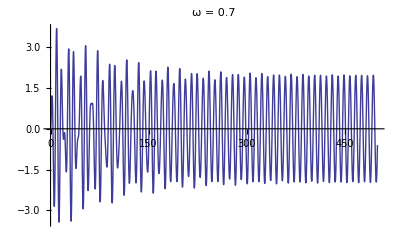

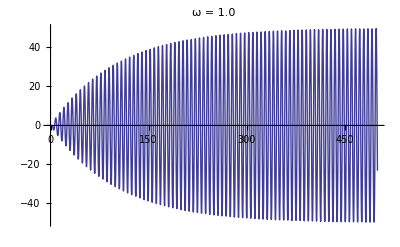

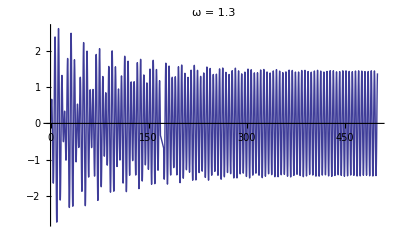

```mathematica
test41 = {ω0->1, F0->1, ω->0.7, γ->0.01};
test42 = {ω0->1, F0->1, ω->1.0, γ->0.01};
test43 = {ω0->1, F0->1, ω->1.3, γ->0.01};
Plot[y37/.test41, {t,0,500}, PlotLabel->"ω = 0.7"]
Plot[y37/.test42, {t,0,500}, PlotLabel->"ω = 1.0"]
Plot[y37/.test43, {t,0,500}, PlotLabel->"ω = 1.3"]
```

### Finding steady state aplitudes and ω_d

```mathematica
ts = Table[i, {i,400,405,.001}];
A1 = Max[Abs[Chop[y37/.{ω0->1, F0->1, ω->0.7, γ->0.01, t->ts}]]]
A2 = Max[Abs[Chop[y37/.{ω0->1, F0->1, ω->1.0, γ->0.01, t->ts}]]]
A3 = Max[Abs[Chop[y37/.{ω0->1, F0->1, ω->1.3, γ->0.01, t->ts}]]]
ωd = ω0 √(1 - γ^2/ω0^2)/.{γ->0.01, ω0->1}
(*Chopping just gets rid of very small imaginary part (on order of 1 * 10^-19) *)
```

1.96797

49.1176

1.45172

0.99995

## P3.5c

```mathematica
ω0=F0=1;
```

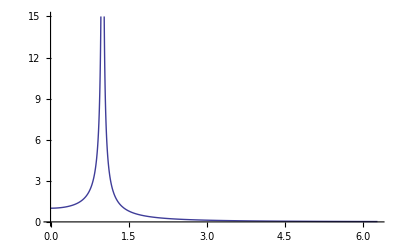

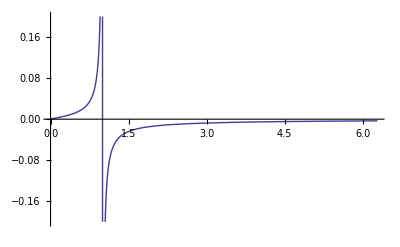

```mathematica
A[ω_, γ_]:=F0/(√((ω0^2 - ω^2)^2 + 4 * γ^2*ω^2))
ϕ[ω_, γ_]:=ArcTan[(2 γ ω)/(ω0^2 - ω^2)]
Plot[A[ω,0.01], {ω, 0,2π}, PlotRange->{0,15}]
Plot[ϕ[ω,0.01], {ω, 0, 2π}, PlotRange->{-.2,.2}]
```

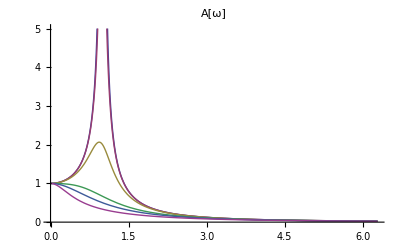

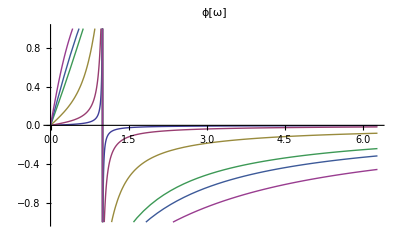

```mathematica
Plot[{A[ω, 0.01], A[ω, 0.05], A[ω, 0.25], A[ω, 0.75], A[ω, 1],A[ω, 1.5]}, {ω, 0,2π}, PlotRange->{0,5}, PlotLabel->"A[ω]",PlotLegend->{"γ = 0.01", "γ = 0.05", "γ = 0.25", "γ = 0.75", "γ = 1", "γ = 1.5"}, LegendPosition->{0,0} ]

Plot[{ϕ[ω, 0.01], ϕ[ω, 0.05], ϕ[ω, 0.25], ϕ[ω, 0.75], ϕ[ω, 1],ϕ[ω, 1.5]}, {ω, 0,2π}, PlotRange->{-1,1}, PlotLabel->"ϕ[ω]",PlotLegend->{"γ = 0.01", "γ = 0.05", "γ = 0.25", "γ = 0.75", "γ = 1", "γ = 1.5"}, LegendPosition->{0,0} ]
```